```mathematica
ClearAll
```

ClearAll

```mathematica
tau1 = Function[t,2.  Sin[0.5 t]]
tau2 = Function[t,  1.5 Cos[1.5 t]] (*check equations*) 
eqsDoublePend = {tau2[t] == 0.3333 m2 l^2 x1''[t] + 0.3333 m2 l x2''[t] + 0.5 m2 l^2 Cos[x2[t]] x1''[t] + 0.5 m2 g l Cos[x1[t] + x2[t]] + 0.5 m2 l^2 Sin[x2[t]] x1'[t]^2 , tau1[t] ==  0.3333 m1 l^2 x1''[t] +1.3333 m2 l x1''[t] +0.3333 m2 l x2''[t] + m2 Cos[x2[t]] l^2 x1''[t] + 0.5 m2 l^2 Cos[x2[t]] x2''[t] - m2 Sin[x2[t]] l^2 x1'[t] x2'[t] - 0.5 m2 Sin[x2[t]] l^2 (x2'[t])^2 + 0.5 m1 g l Cos[x1[t]] + 0.5 m2 g l Cos[x1[t] + x2[t]] + m2 g l Cos[x1[t]]}
```

Function[t,2. Sin[0.5 t]]

Function[t,1.5 Cos[1.5 t]]

{1.5 Cos[1.5 t]==0.5 g l m2 Cos[x1[t]+x2[t]]+0.5 l^2 m2 Sin[x2[t]] x1'[t]^2+0.3333 l^2 m2 x1''[t]+0.5 l^2 m2 Cos[x2[t]] x1''[t]+0.3333 l m2 x2''[t],2. Sin[0.5 t]==0.5 g l m1 Cos[x1[t]]+g l m2 Cos[x1[t]]+0.5 g l m2 Cos[x1[t]+x2[t]]-l^2 m2 Sin[x2[t]] x1'[t] x2'[t]-0.5 l^2 m2 Sin[x2[t]] x2'[t]^2+0.3333 l^2 m1 x1''[t]+1.3333 l m2 x1''[t]+l^2 m2 Cos[x2[t]] x1''[t]+0.3333 l m2 x2''[t]+0.5 l^2 m2 Cos[x2[t]] x2''[t]}

```mathematica
rules = {m1->1., m2->0.001, l->1., g->9.81}
```

{m1→1.,m2→0.001,l→1.,g→9.81}

```mathematica
ndsol = NDSolve[(eqsDoublePend/.rules)~Join~{x1[0]==0. Degree,x2[0] == 0. Degree,x1'[0]==0., x2'[0] == 0.},{x1[t], x2[t], x1'[t], x2'[t]},{t, 0., 10.}][[1]]
```

{x1[t]→InterpolatingFunction[{{0., 10.}}, <>][t],x2[t]→InterpolatingFunction[{{0., 10.}}, <>][t],x1'[t]→InterpolatingFunction[{{0., 10.}}, <>][t],x2'[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}

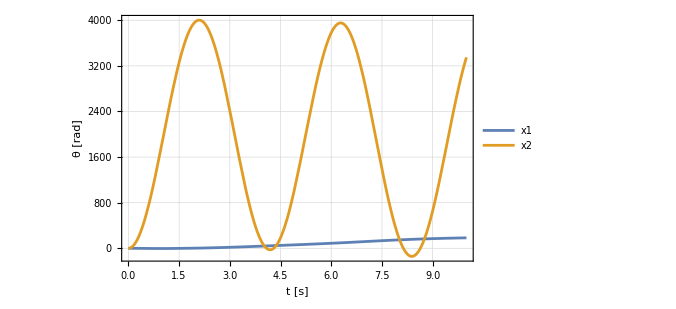

```mathematica
Plot[Evaluate[{x1[t], x2[t]}/.ndsol],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ [rad]"}, PlotLegends->{"x1", "x2"}]
```

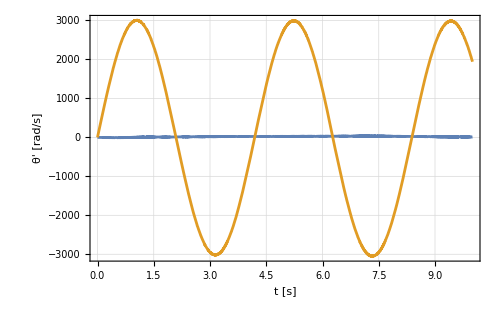

```mathematica
Plot[Evaluate[{x1'[t], x2'[t]}/.ndsol],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ' [rad/s]"}]
```

```mathematica
doubles = Solve[eqsDoublePend, {x1''[t], x2''[t]}]/.rules/.ndsol
```

{{x1''[t]→-((-1. (-0.0003333-0.0005 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]]) (1.5 Cos[1.5 t]-0.004905 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]+InterpolatingFunction[{{0., 10.}}, <>][t]]-0.0005 Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] (InterpolatingFunction[{{0., 10.}}, <>][t])^2)-0.0003333 (-4.91481 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]]-0.004905 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]+InterpolatingFunction[{{0., 10.}}, <>][t]]+2. Sin[0.5 t]+0.001 Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] InterpolatingFunction[{{0., 10.}}, <>][t] InterpolatingFunction[{{0., 10.}}, <>][t]+0.0005 Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] (InterpolatingFunction[{{0., 10.}}, <>][t])^2))/(0.000111422-2.5×10^-7 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]]^2)),x2''[t]→(2000. (-1.0039 Cos[1.5 t]-0.00327621 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]]-0.003 Cos[1.5 t] Cos[InterpolatingFunction[{{0., 10.}}, <>][t]]-0.00491481 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]] Cos[InterpolatingFunction[{{0., 10.}}, <>][t]]+0.00327948 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]+InterpolatingFunction[{{0., 10.}}, <>][t]]+4.905×10^-6 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]] Cos[InterpolatingFunction[{{0., 10.}}, <>][t]+InterpolatingFunction[{{0., 10.}}, <>][t]]+0.0013332 Sin[0.5 t]+0.002 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]] Sin[0.5 t]+0.000334633 Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] (InterpolatingFunction[{{0., 10.}}, <>][t])^2+1.×10^-6 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]] Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] (InterpolatingFunction[{{0., 10.}}, <>][t])^2+6.666×10^-7 Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] InterpolatingFunction[{{0., 10.}}, <>][t] InterpolatingFunction[{{0., 10.}}, <>][t]+1.×10^-6 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]] Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] InterpolatingFunction[{{0., 10.}}, <>][t] InterpolatingFunction[{{0., 10.}}, <>][t]+3.333×10^-7 Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] (InterpolatingFunction[{{0., 10.}}, <>][t])^2+5.×10^-7 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]] Sin[InterpolatingFunction[{{0., 10.}}, <>][t]] (InterpolatingFunction[{{0., 10.}}, <>][t])^2))/(-0.445689+0.001 Cos[InterpolatingFunction[{{0., 10.}}, <>][t]]^2)}}

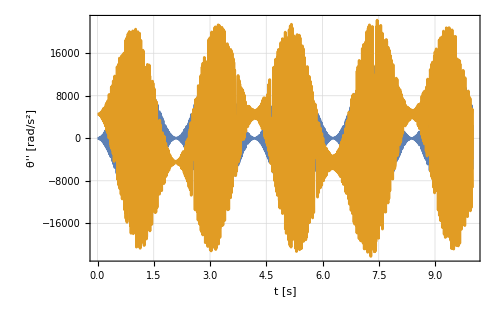

```mathematica
Plot[Evaluate[{x1''[t], x2''[t]}/.doubles],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ'' [rad/s^2]"}]
```

```mathematica
ClearAll@results
results[sols_, time_, expr_] := Module[{sol, sol2, solF},
sol = sols/.t->time;
sol2 = expr/.t->time;
solF = Join[sol[[All, 2]], sol2[[1, All, 2]]];
solF]
```

```mathematica
var = ndsol/.t->0.5
```

{x1[0.5]→-2.03787,x2[0.5]→539.417,x1'[0.5]→-8.00279,x2'[0.5]→2055.3}

```mathematica
var[[All, 2]]
```

{-2.03787,539.417,-8.00279,2055.3}

```mathematica
var2 = doubles/.t->0.5
```

{{x1''[0.5]→-5051.61,x2''[0.5]→12927.5}}

```mathematica
var2[[1, All, 2]]
```

{-5051.61,12927.5}

```mathematica
sol1 = results[ndsol, 0.5, doubles]
```

{-2.03787,539.417,-8.00279,2055.3,-5051.61,12927.5}

```mathematica
finalRes = Table[{time,results[ndsol,time, doubles]},{time,0., 10., 10./1000.}]
```

```mathematica
ndsol/.t->10
```

{x1[10]→183.598,x2[10]→3349.39,x1'[10]→7.94399,x2'[10]→1942.38}

```mathematica
doubles/.t->10
```

{{x1''[10]→2494.63,x2''[10]→-9315.8}}

```mathematica
Length@finalRes[[All, 2]]
```

1001

```mathematica
finalRes[[1]]
```

{0.,{0.,0.,0.,-2.71051×10^-20,-25.9562,4550.63}}

```mathematica
Short@finalRes[[All, 2]]
```

{{0.,0.,0.,-2.71051×10^-20,-25.9562,4550.63},«999»,{183.598,3349.39,«18»,«18»,2494.63,-9315.8}}

```mathematica
Export["A:\\uni\\masters nu\\RA\\pythonCode\\data\\planarDoublePend2.csv",finalRes[[All, 2]]]
```

A:\uni\masters nu\RA\pythonCode\data\planarDoublePend2.csv

```mathematica
Import[%]
```

```mathematica
Directory[]
```

C:\Users\alizhan

```mathematica
ClearAll@{x1, x2}
```

```mathematica
tau1 = Function[t,2.  Sin[0.5 t]]
tau2 = Function[t,  0.001 Cos[1.5 t]] (*check equations*) 
eqsDoublePend2 = { tau1[t] ==  0.3333 m1 l^2 x1''[t] +1.3333 m2 l x1''[t] +0.3333 m2 l x2''[t] + m2 Cos[x2[t]] l^2 x1''[t] + 0.5 m2 l^2 Cos[x2[t]] x2''[t] - m2 Sin[x2[t]] l^2 x1'[t] x2'[t] - 0.5 m2 Sin[x2[t]] l^2 (x2'[t])^2 + 0.5 m1 g l Cos[x1[t]] + 0.5 m2 g l Cos[x1[t] + x2[t]] + m2 g l Cos[x1[t]]}
```

Function[t,2. Sin[0.5 t]]

Function[t,0.001 Cos[1.5 t]]

{2. Sin[0.5 t]==0.5 g l m1 Cos[x1[t]]+g l m2 Cos[x1[t]]+0.5 g l m2 Cos[x1[t]+x2[t]]-l^2 m2 Sin[x2[t]] x1'[t] x2'[t]-0.5 l^2 m2 Sin[x2[t]] x2'[t]^2+0.3333 l^2 m1 x1''[t]+1.3333 l m2 x1''[t]+l^2 m2 Cos[x2[t]] x1''[t]+0.3333 l m2 x2''[t]+0.5 l^2 m2 Cos[x2[t]] x2''[t]}

```mathematica
rules2 = {m1->1., m2->0., l->1., g->9.81}
```

{m1→1.,m2→0.,l→1.,g→9.81}

```mathematica
ndsol2 = NDSolve[(eqsDoublePend2/.rules2)~Join~{x1[0]==0 Degree,x1'[0]==0},{x1[t], x1'[t]},{t, 0, 10}][[1]]
```

{x1[t]→InterpolatingFunction[…][t],x1'[t]→InterpolatingFunction[…][t]}

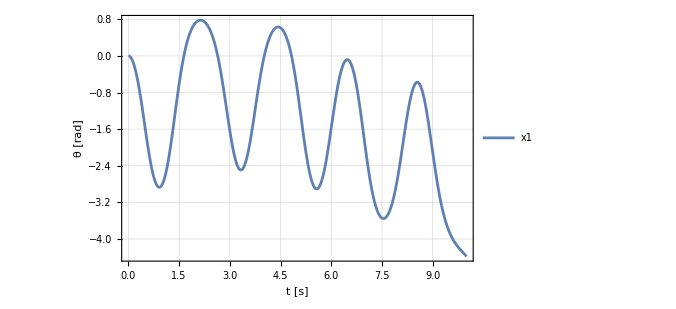

```mathematica
Plot[Evaluate[{x1[t]}/.ndsol2],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ [rad]"}, PlotLegends->{"x1", "x2"}]
```

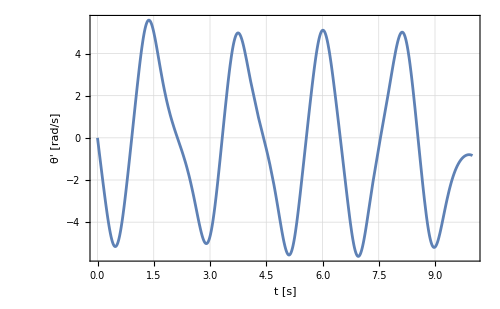

```mathematica
Plot[Evaluate[{x1'[t]}/.ndsol2],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ' [rad/s]"}]
```

```mathematica
doubles2 = Solve[eqsDoublePend2, {x1''[t]}]/.rules2/.ndsol2
```

{{x1''[t]→-3.0003 (0.+4.905 Cos[InterpolatingFunction[…][t]]-2. Sin[0.5 t])}}

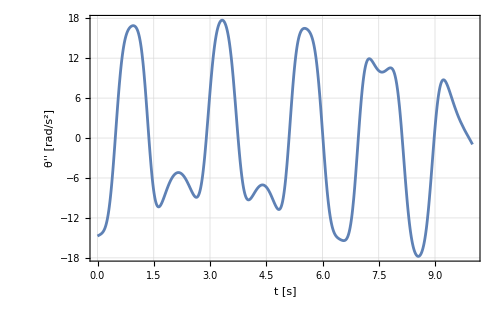

```mathematica
Plot[Evaluate[{x1''[t]}/.doubles2],{t,0,10},Frame->True,GridLines->Automatic,LabelStyle->Directive[20, Black],ImageSize->500,FrameLabel->{"t [s]","θ'' [rad/s^2]"}]
```

```mathematica
ClearAll@results
results[sols_, time_, expr_] := Module[{sol, sol2, solF},
sol = sols/.t->time;
sol2 = expr/.t->time;
solF = Join[sol[[All, 2]], sol2[[1, All, 2]]];
solF]
```

```mathematica
sol1 = results[ndsol2, 0.5, doubles2]
```

{-1.60649,-5.1311,2.00972}

```mathematica
doubles2/.t->0.5
```

{{x1''[0.5]→2.00972}}

```mathematica
ndsol2/.t->0.5
```

{x1[0.5]→-1.60649,x1'[0.5]→-5.1311}

```mathematica
finalRes2 = Table[{time,results[ndsol2,time, doubles2]},{time,0., 10., 10./1000.}]
```

```mathematica
Length@finalRes2[[All, 2]]
```

1001

```mathematica
Short@finalRes2[[All, 2]]
```

{{0.,-5.42101×10^-20,-14.7165},«999»,{-4.38022,-0.841747,-0.95512}}

```mathematica
finalRes2[[1]]
```

{0.,{0.,-5.42101×10^-20,-14.7165}}

```mathematica
Export["A:\\uni\\masters nu\\RA\\pythonCode\\data\\planarSinglePend2.csv",finalRes2[[All, 2]]]
```

A:\uni\masters nu\RA\pythonCode\data\planarSinglePend2.csv

```mathematica
Import[%]
```

{{0.,-5.42101×10^-20,-14.7165},{-0.00073531,-0.147017,-14.6865},{-0.0029393,-0.293729,-14.6564},{-0.0066089,-0.440142,-14.6261},{-0.0117411,-0.58625,-14.5955},{-0.0183329,-0.732048,-14.564},{-0.026381,-0.877527,-14.5314},{-0.0358823,-1.02267,-14.497},{-0.0468332,-1.16746,-14.4604},{-0.0592302,-1.31187,-14.4207},{-0.0730692,-1.45586,-14.3773},{-0.0883459,-1.5994,-14.3292},{-0.105055,-1.74243,-14.2755},{-0.123193,-1.88489,-14.2152},{-0.142751,-2.0267,-14.1471},{-0.163724,-2.1678,-14.07},{-0.186104,-2.30807,-13.9828},{-0.209883,-2.44742,-13.8841},{-0.235049,-2.58571,-13.7725},{-0.261593,-2.72282,-13.6466},{-0.289501,-2.85859,-13.505},{-0.31876,-2.99286,-13.3462},{-0.349353,-3.12545,-13.1688},{-0.381262,-3.25617,-12.9712},{-0.414469,-3.3848,-12.7521},{-0.448951,-3.51113,-12.51},{-0.484683,-3.63492,-12.2436},{-0.52164,-3.75592,-11.9516},{-0.559792,-3.87387,-11.6329},{-0.599106,-3.98849,-11.2864},{-0.639549,-4.0995,-10.9113},{-0.681083,-4.20661,-10.5067},{-0.723668,-4.30953,-10.0723},{-0.767259,-4.40796,-9.60754},{-0.811811,-4.50158,-9.11247},{-0.857274,-4.59011,-8.5872},{-0.903595,-4.67323,-8.03212},{-0.950719,-4.75065,-7.44792},{-0.998588,-4.82209,-6.83555},{-1.04714,-4.88727,-6.19625},{-1.09631,-4.94593,-5.53153},{-1.14604,-4.99782,-4.84317},{-1.19624,-5.04272,-4.13321},{-1.24687,-5.08042,-3.40396},{-1.29783,-5.11075,-2.65791},{-1.34906,-5.13354,-1.89778},{-1.40047,-5.14866,-1.12644},{-1.452,-5.15604,-0.346898},{-1.50357,-5.15559,0.437749},{-1.55509,-5.14728,1.22434},{-1.60649,-5.1311,2.00972},{-1.65769,-5.1071,2.79072},{-1.7086,-5.07531,3.56427},{-1.75917,-5.03585,4.32739},{-1.8093,-4.98881,5.07724},{-1.85892,-4.93435,5.81115},{-1.90796,-4.87265,6.52666},{-1.95635,-4.80389,7.22153},{-2.00401,-4.72829,7.89376},{-2.05089,-4.6461,8.54161},{-2.09691,-4.55755,9.16362},{-2.14202,-4.46291,9.75859},{-2.18615,-4.36247,10.3256},{-2.22925,-4.2565,10.864},{-2.27127,-4.14528,11.3735},{-2.31214,-4.02912,11.8538},{-2.35183,-3.90831,12.3051},{-2.39029,-3.78312,12.7276},{-2.42748,-3.65385,13.122},{-2.46336,-3.52077,13.4888},{-2.49788,-3.38416,13.8289},{-2.53103,-3.24428,14.1433},{-2.56276,-3.10138,14.433},{-2.59305,-2.95569,14.6992},{-2.62187,-2.80746,14.9431},{-2.64919,-2.6569,15.166},{-2.675,-2.50421,15.3691},{-2.69927,-2.34958,15.5537},{-2.72198,-2.19319,15.7211},{-2.74313,-2.03521,15.8726},{-2.76268,-1.87579,16.0093},{-2.78064,-1.71507,16.1325},{-2.79698,-1.55318,16.2431},{-2.8117,-1.39025,16.3423},{-2.82478,-1.22637,16.4309},{-2.83622,-1.06166,16.5098},{-2.84601,-0.896205,16.5797},{-2.85414,-0.730093,16.6414},{-2.86061,-0.563404,16.6952},{-2.86541,-0.396213,16.7418},{-2.86853,-0.228592,16.7813},{-2.86998,-0.0606095,16.814},{-2.86975,0.107666,16.84},{-2.86783,0.276168,16.8592},{-2.86422,0.444828,16.8716},{-2.85893,0.613576,16.8768},{-2.85195,0.782338,16.8744},{-2.84328,0.951037,16.864},{-2.83293,1.11959,16.845},{-2.82089,1.28791,16.8166},{-2.80717,1.45589,16.778},{-2.79178,1.62343,16.7283},{-2.77471,1.79041,16.6664},{-2.75597,1.95671,16.5913},{-2.73557,2.12219,16.5016},{-2.71353,2.28669,16.3962},{-2.68984,2.45006,16.2737},{-2.66453,2.61211,16.1327},{-2.63761,2.77265,15.9718},{-2.60909,2.93147,15.7896},{-2.57898,3.08836,15.5846},{-2.54733,3.24308,15.3554},{-2.51413,3.39539,15.1007},{-2.47943,3.54501,14.8191},{-2.44324,3.69168,14.5095},{-2.4056,3.8351,14.1707},{-2.36655,3.97499,13.8018},{-2.32612,4.11103,13.402},{-2.28434,4.24292,12.9707},{-2.24127,4.37034,12.5076},{-2.19695,4.49297,12.0126},{-2.15143,4.61049,11.4857},{-2.10476,4.72258,10.9275},{-2.057,4.82894,10.3387},{-2.0082,4.92925,9.72033},{-1.95843,5.02325,9.07381},{-1.90776,5.11064,8.40082},{-1.85624,5.19118,7.7034},{-1.80396,5.26464,6.98386},{-1.75098,5.3308,6.24484},{-1.69737,5.38948,5.48921},{-1.64321,5.44053,4.72009},{-1.58858,5.48385,3.94082},{-1.53356,5.51933,3.15488},{-1.47822,5.54693,2.36589},{-1.42265,5.56665,1.57752},{-1.36692,5.5785,0.793489},{-1.3111,5.58255,0.0174885},{-1.25529,5.57889,-0.746865},{-1.19955,5.56766,-1.49607},{-1.14396,5.54903,-2.22679},{-1.0886,5.5232,-2.93588},{-1.03352,5.49039,-3.62044},{-0.97881,5.45088,-4.27784},{-0.924526,5.40493,-4.90575},{-0.870732,5.35287,-5.50212},{-0.817488,5.295,-6.06527},{-0.76485,5.23168,-6.5938},{-0.712872,5.16324,-7.08669},{-0.661601,5.09007,-7.5432},{-0.611085,5.0125,-7.96293},{-0.561365,4.93093,-8.34578},{-0.512478,4.84571,-8.69193},{-0.464461,4.75721,-9.00182},{-0.417344,4.66579,-9.27611},{-0.371154,4.57181,-9.5157},{-0.325915,4.47559,-9.72167},{-0.281648,4.37748,-9.89525},{-0.238371,4.27779,-10.0378},{-0.196097,4.17682,-10.1508},{-0.154838,4.07487,-10.2358},{-0.114602,3.97219,-10.2945},{-0.0753955,3.86906,-10.3285},{-0.0372216,3.7657,-10.3395},{-0.0000814932,3.66234,-10.3292},{0.0360259,3.55918,-10.2992},{0.0711034,3.45642,-10.2513},{0.105156,3.35421,-10.187},{0.13819,3.25273,-10.1079},{0.170213,3.1521,-10.0155},{0.201235,3.05245,-9.91137},{0.231266,2.95391,-9.7968},{0.260317,2.85655,-9.67314},{0.288401,2.76047,-9.54165},{0.315531,2.66574,-9.40351},{0.341721,2.57242,-9.25983},{0.366984,2.48056,-9.11166},{0.391337,2.3902,-8.95995},{0.414793,2.30137,-8.80561},{0.437369,2.21409,-8.64947},{0.45908,2.12838,-8.4923},{0.479942,2.04424,-8.33481},{0.499971,1.96168,-8.17763},{0.519181,1.88069,-8.02137},{0.53759,1.80125,-7.86656},{0.555211,1.72335,-7.71369},{0.572062,1.64697,-7.56321},{0.588156,1.57208,-7.41552},{0.603508,1.49865,-7.27097},{0.618133,1.42665,-7.12989},{0.632046,1.35604,-6.99257},{0.645259,1.28678,-6.85927},{0.657786,1.21884,-6.73021},{0.66964,1.15216,-6.6056},{0.680833,1.08671,-6.48561},{0.691378,1.02243,-6.3704},{0.701285,0.959286,-6.2601},{0.710567,0.897216,-6.15484},{0.719233,0.836173,-6.05471},{0.727294,0.776104,-5.9598},{0.734758,0.716959,-5.87018},{0.741636,0.658683,-5.78593},{0.747935,0.601222,-5.70707},{0.753663,0.544523,-5.63367},{0.758828,0.488531,-5.56575},{0.763436,0.43319,-5.50334},{0.767493,0.378446,-5.44645},{0.771006,0.324242,-5.39511},{0.77398,0.270525,-5.34931},{0.776418,0.217238,-5.30908},{0.778326,0.164325,-5.27439},{0.779706,0.111731,-5.24526},{0.780561,0.0594011,-5.22167},{0.780895,0.00727929,-5.20362},{0.780707,-0.0446896,-5.19109},{0.780001,-0.0965608,-5.18406},{0.778776,-0.148389,-5.18252},{0.777033,-0.200229,-5.18645},{0.774771,-0.252136,-5.19582},{0.77199,-0.304164,-5.2106},{0.768688,-0.356366,-5.23077},{0.764862,-0.408797,-5.25629},{0.760511,-0.46151,-5.28712},{0.755631,-0.514557,-5.32322},{0.750218,-0.567991,-5.36455},{0.744269,-0.621865,-5.41104},{0.737779,-0.676229,-5.46264},{0.730743,-0.731135,-5.51929},{0.723155,-0.786632,-5.58091},{0.715008,-0.842769,-5.64742},{0.706297,-0.899596,-5.71872},{0.697014,-0.957159,-5.79472},{0.687151,-1.01551,-5.87529},{0.676701,-1.07468,-5.96031},{0.665655,-1.13473,-6.04963},{0.654003,-1.19569,-6.1431},{0.641738,-1.2576,-6.24054},{0.628848,-1.32051,-6.34174},{0.615324,-1.38445,-6.4465},{0.601156,-1.44945,-6.55457},{0.586332,-1.51555,-6.66568},{0.570841,-1.58277,-6.77953},{0.554672,-1.65115,-6.89582},{0.537814,-1.7207,-7.01418},{0.520254,-1.79144,-7.13422},{0.501981,-1.86339,-7.25552},{0.482983,-1.93655,-7.37761},{0.463246,-2.01094,-7.5},{0.44276,-2.08655,-7.62213},{0.421511,-2.16338,-7.74342},{0.399488,-2.24141,-7.86322},{0.376679,-2.32064,-7.98085},{0.353071,-2.40102,-8.09557},{0.328655,-2.48254,-8.20659},{0.303417,-2.56514,-8.31306},{0.277348,-2.64878,-8.41408},{0.250438,-2.7334,-8.5087},{0.222677,-2.81893,-8.59592},{0.194057,-2.90529,-8.67466},{0.164569,-2.99239,-8.74381},{0.134207,-3.08013,-8.80221},{0.102965,-3.16839,-8.84865},{0.0708379,-3.25706,-8.88187},{0.0378229,-3.34598,-8.90059},{0.00391791,-3.43502,-8.90349},{-0.0308773,-3.52399,-8.88921},{-0.0665612,-3.61274,-8.85641},{-0.103131,-3.70106,-8.80372},{-0.14058,-3.78874,-8.7298},{-0.178903,-3.87558,-8.63331},{-0.218088,-3.96133,-8.51296},{-0.258125,-4.04575,-8.3675},{-0.298998,-4.12859,-8.19576},{-0.34069,-4.20958,-7.99665},{-0.383182,-4.28843,-7.76919},{-0.426451,-4.36486,-7.51251},{-0.470471,-4.43858,-7.22589},{-0.515213,-4.50928,-6.90877},{-0.560645,-4.57665,-6.56077},{-0.606733,-4.64039,-6.18169},{-0.65344,-4.70018,-5.77155},{-0.700723,-4.75572,-5.33061},{-0.748539,-4.80669,-4.85933},{-0.796841,-4.85281,-4.35844},{-0.845578,-4.89377,-3.82892},{-0.894698,-4.92929,-3.27196},{-0.944145,-4.95912,-2.68905},{-0.99386,-4.98299,-2.08187},{-1.04378,-5.00068,-1.45235},{-1.09385,-5.01197,-0.802649},{-1.144,-5.01668,-0.135088},{-1.19416,-5.01462,0.547825},{-1.24427,-5.00568,1.24344},{-1.29425,-4.98972,1.94899},{-1.34404,-4.96667,2.66164},{-1.39356,-4.93648,3.37848},{-1.44275,-4.8991,4.0966},{-1.49152,-4.85455,4.81311},{-1.53981,-4.80285,5.52515},{-1.58755,-4.74407,6.22999},{-1.63467,-4.67829,6.92496},{-1.6811,-4.60561,7.60757},{-1.72676,-4.52618,8.27549},{-1.7716,-4.44016,8.92656},{-1.81554,-4.34771,9.55883},{-1.85853,-4.24905,10.1706},{-1.90051,-4.14438,10.7603},{-1.9414,-4.03392,11.3268},{-1.98116,-3.91792,11.8689},{-2.01974,-3.79663,12.3858},{-2.05708,-3.67029,12.877},{-2.09313,-3.53918,13.342},{-2.12785,-3.40354,13.7807},{-2.16119,-3.26365,14.193},{-2.19311,-3.11977,14.5791},{-2.22357,-2.97216,14.9392},{-2.25254,-2.82107,15.2739},{-2.27998,-2.66676,15.5836},{-2.30587,-2.50948,15.8689},{-2.33016,-2.34946,16.1306},{-2.35285,-2.18694,16.3693},{-2.37389,-2.02215,16.5858},{-2.39328,-1.8553,16.7808},{-2.41099,-1.6866,16.9552},{-2.42701,-1.51626,17.1097},{-2.44131,-1.34447,17.2449},{-2.45389,-1.17143,17.3616},{-2.46474,-0.997301,17.4604},{-2.47384,-0.822275,17.5418},{-2.48118,-0.646521,17.6063},{-2.48677,-0.470205,17.6542},{-2.49058,-0.293491,17.6859},{-2.49264,-0.11654,17.7016},{-2.49292,0.0604875,17.7013},{-2.49143,0.237433,17.6852},{-2.48817,0.414137,17.653},{-2.48314,0.59044,17.6047},{-2.47636,0.766178,17.54},{-2.46782,0.941185,17.4586},{-2.45754,1.11529,17.3599},{-2.44552,1.28832,17.2435},{-2.43178,1.4601,17.1088},{-2.41632,1.63044,16.9552},{-2.39917,1.79914,16.7819},{-2.38035,1.96601,16.5883},{-2.35986,2.13084,16.3736},{-2.33774,2.29341,16.137},{-2.314,2.4535,15.8778},{-2.28868,2.61089,15.5953},{-2.26179,2.76533,15.2887},{-2.23338,2.91658,14.9574},{-2.20347,3.06439,14.601},{-2.17211,3.20851,14.219},{-2.13932,3.34868,13.8109},{-2.10515,3.48464,13.3768},{-2.06964,3.61613,12.9164},{-2.03284,3.74288,12.43},{-1.9948,3.86465,11.918},{-1.95556,3.98116,11.3807},{-1.91519,4.09218,10.8191},{-1.87374,4.19746,10.234},{-1.83126,4.29679,9.62673},{-1.78782,4.38993,8.99861},{-1.74349,4.47669,8.35133},{-1.69831,4.5569,7.68674},{-1.65237,4.63038,7.00691},{-1.60573,4.69699,6.3141},{-1.55845,4.75663,5.61074},{-1.51062,4.80918,4.8994},{-1.46229,4.8546,4.18278},{-1.41355,4.89283,3.46365},{-1.36446,4.92387,2.74486},{-1.3151,4.94774,2.02928},{-1.26553,4.96448,1.31978},{-1.21583,4.97416,0.619177},{-1.16607,4.9769,-0.0697776},{-1.11632,4.97281,-0.744439},{-1.06664,4.96207,-1.4023},{-1.0171,4.94483,-2.041},{-0.96776,4.92132,-2.65839},{-0.91869,4.89174,-3.2525},{-0.869945,4.85635,-3.8216},{-0.821581,4.8154,-4.36417},{-0.773654,4.76916,-4.87897},{-0.726215,4.71792,-5.36497},{-0.679312,4.66196,-5.82139},{-0.632991,4.60159,-6.24771},{-0.587294,4.53711,-6.64362},{-0.542261,4.46882,-7.00906},{-0.497929,4.39703,-7.34415},{-0.454331,4.32203,-7.64924},{-0.411498,4.24414,-7.92484},{-0.369457,4.16363,-8.17163},{-0.328233,4.0808,-8.39044},{-0.287848,3.99591,-8.58221},{-0.248321,3.90924,-8.74802},{-0.209668,3.82104,-8.889},{-0.171904,3.73154,-9.00639},{-0.135041,3.64098,-9.10146},{-0.0990875,3.54958,-9.17554},{-0.0640515,3.45754,-9.22996},{-0.0299383,3.36504,-9.2661},{0.00324846,3.27227,-9.28531},{0.0355068,3.17939,-9.28894},{0.0668364,3.08654,-9.27831},{0.0972382,2.99387,-9.25475},{0.126715,2.90149,-9.21951},{0.155269,2.80951,-9.17382},{0.182907,2.71804,-9.11888},{0.209632,2.62716,-9.05582},{0.235452,2.53695,-8.98572},{0.260373,2.44747,-8.90963},{0.284404,2.35877,-8.82852},{0.307552,2.27091,-8.74333},{0.329825,2.18391,-8.65493},{0.351233,2.09782,-8.56414},{0.371784,2.01264,-8.47173},{0.391489,1.92839,-8.37842},{0.410355,1.84507,-8.28489},{0.428393,1.76269,-8.19175},{0.445612,1.68123,-8.09959},{0.462021,1.60069,-8.00894},{0.477629,1.52105,-7.92029},{0.492445,1.44228,-7.8341},{0.506477,1.36435,-7.75079},{0.519735,1.28725,-7.67075},{0.532225,1.21093,-7.59432},{0.543956,1.13535,-7.52182},{0.554934,1.06048,-7.45356},{0.565167,0.986264,-7.38979},{0.574661,0.912665,-7.33076},{0.583422,0.839632,-7.27669},{0.591456,0.767114,-7.22778},{0.598766,0.695059,-7.18421},{0.605358,0.623412,-7.14612},{0.611236,0.552117,-7.11368},{0.616402,0.481119,-7.08699},{0.620859,0.410358,-7.06618},{0.624609,0.339775,-7.05134},{0.627655,0.269311,-7.04255},{0.629996,0.198904,-7.03989},{0.631633,0.128492,-7.04339},{0.632565,0.0580151,-7.05312},{0.632793,-0.0125908,-7.0691},{0.632313,-0.0833879,-7.09136},{0.631124,-0.154439,-7.11989},{0.629223,-0.225807,-7.15469},{0.626607,-0.297554,-7.19575},{0.623271,-0.369742,-7.24302},{0.61921,-0.442435,-7.29647},{0.61442,-0.515692,-7.35604},{0.608894,-0.589575,-7.42164},{0.602626,-0.664145,-7.49318},{0.595609,-0.739459,-7.57056},{0.587834,-0.815575,-7.65363},{0.579295,-0.89255,-7.74224},{0.56998,-0.970438,-7.83623},{0.559883,-1.04929,-7.93538},{0.548991,-1.12916,-8.03947},{0.537296,-1.2101,-8.14825},{0.524786,-1.29214,-8.26142},{0.511449,-1.37534,-8.37866},{0.497275,-1.45973,-8.49962},{0.48225,-1.54534,-8.6239},{0.466364,-1.63221,-8.75106},{0.449602,-1.72037,-8.88061},{0.431952,-1.80983,-9.01203},{0.413401,-1.90062,-9.14472},{0.393935,-1.99273,-9.27806},{0.373542,-2.08618,-9.41134},{0.352207,-2.18095,-9.54381},{0.329918,-2.27705,-9.67466},{0.306662,-2.37444,-9.80301},{0.282425,-2.4731,-9.9279},{0.257196,-2.57298,-10.0483},{0.230962,-2.67404,-10.1632},{0.203711,-2.77622,-10.2713},{0.175434,-2.87944,-10.3715},{0.146119,-2.98362,-10.4624},{0.115759,-3.08866,-10.5427},{0.0843436,-3.19444,-10.611},{0.0518678,-3.30083,-10.6657},{0.0183254,-3.4077,-10.7053},{-0.0162873,-3.51488,-10.7282},{-0.0519727,-3.6222,-10.7327},{-0.0887311,-3.72947,-10.7173},{-0.126561,-3.83647,-10.6801},{-0.165459,-3.94299,-10.6196},{-0.205419,-4.04878,-10.5341},{-0.246431,-4.15359,-10.4218},{-0.288486,-4.25713,-10.2814},{-0.331569,-4.35911,-10.1111},{-0.375662,-4.45924,-9.90965},{-0.420746,-4.5572,-9.67575},{-0.466798,-4.65265,-9.40824},{-0.51379,-4.74525,-9.10616},{-0.561692,-4.83465,-8.76875},{-0.610471,-4.9205,-8.39546},{-0.660089,-5.00244,-7.98601},{-0.710506,-5.0801,-7.54038},{-0.761676,-5.15313,-7.05883},{-0.813551,-5.22116,-6.54195},{-0.866081,-5.28385,-5.99064},{-0.91921,-5.34086,-5.40611},{-0.972878,-5.39187,-4.7899},{-1.02703,-5.43656,-4.14391},{-1.08159,-5.47466,-3.4703},{-1.1365,-5.50588,-2.77156},{-1.19168,-5.53001,-2.05046},{-1.24707,-5.54683,-1.31},{-1.30259,-5.55616,-0.553416},{-1.35817,-5.55785,0.215902},{-1.41372,-5.55181,0.994413},{-1.46918,-5.53795,1.77849},{-1.52446,-5.51623,2.56446},{-1.57948,-5.48666,3.34865},{-1.63416,-5.44928,4.12746},{-1.68844,-5.40415,4.89738},{-1.74222,-5.35137,5.65502},{-1.79544,-5.2911,6.39722},{-1.84802,-5.22349,7.12101},{-1.89989,-5.14875,7.82367},{-1.95097,-5.06709,8.50278},{-2.00121,-4.97878,9.15619},{-2.05053,-4.88406,9.78209},{-2.09887,-4.78323,10.379},{-2.14617,-4.67658,10.9456},{-2.19238,-4.56442,11.4812},{-2.23744,-4.44706,11.9852},{-2.28131,-4.32482,12.4573},{-2.32392,-4.19803,12.8974},{-2.36525,-4.06698,13.3059},{-2.40525,-3.93201,13.6833},{-2.44388,-3.79342,14.0302},{-2.48111,-3.6515,14.3476},{-2.5169,-3.50656,14.6365},{-2.55123,-3.35887,14.8981},{-2.58407,-3.20869,15.1335},{-2.6154,-3.05628,15.3443},{-2.64519,-2.90188,15.5318},{-2.67343,-2.74571,15.6975},{-2.7001,-2.588,15.8427},{-2.72518,-2.42892,15.9691},{-2.74867,-2.26867,16.0779},{-2.77055,-2.10742,16.1706},{-2.79082,-1.94531,16.2485},{-2.80946,-1.78249,16.3128},{-2.82646,-1.61909,16.3649},{-2.84184,-1.45523,16.4058},{-2.85557,-1.29101,16.4365},{-2.86766,-1.12653,16.4579},{-2.8781,-0.961882,16.471},{-2.88689,-0.79714,16.4763},{-2.89404,-0.632379,16.4746},{-2.89954,-0.46767,16.4663},{-2.90339,-0.303074,16.4518},{-2.9056,-0.138654,16.4314},{-2.90617,0.0255341,16.4052},{-2.90509,0.189432,16.3734},{-2.90238,0.352983,16.3358},{-2.89804,0.516128,16.2923},{-2.89206,0.678807,16.2425},{-2.88446,0.840956,16.1861},{-2.87524,1.00251,16.1226},{-2.86441,1.16338,16.0514},{-2.85198,1.32351,15.9718},{-2.83795,1.48279,15.8829},{-2.82233,1.64113,15.7838},{-2.80513,1.79843,15.6737},{-2.78636,1.95456,15.5514},{-2.76604,2.10941,15.4158},{-2.74418,2.26283,15.2658},{-2.72079,2.41468,15.1001},{-2.69589,2.56478,14.9174},{-2.6695,2.71296,14.7165},{-2.64164,2.85904,14.4961},{-2.61233,3.00282,14.2548},{-2.58159,3.14407,13.9914},{-2.54945,3.28257,13.7048},{-2.51595,3.41808,13.3937},{-2.4811,3.55036,13.0571},{-2.44495,3.67913,12.6941},{-2.40753,3.80415,12.3037},{-2.36888,3.92512,11.8854},{-2.32904,4.04176,11.4386},{-2.28806,4.15379,10.9631},{-2.24599,4.26092,10.4587},{-2.20286,4.36287,9.92556},{-2.15875,4.45934,9.36409},{-2.11369,4.55006,8.77491},{-2.06777,4.63475,8.15892},{-2.02102,4.71315,7.51731},{-1.97352,4.78502,6.8515},{-1.92534,4.85011,6.16321},{-1.87655,4.90821,5.45438},{-1.8272,4.95913,4.72722},{-1.77739,5.0027,3.98414},{-1.72717,5.03877,3.22776},{-1.67664,5.06722,2.46086},{-1.62585,5.08796,1.68635},{-1.5749,5.10093,0.907249},{-1.52386,5.1061,0.126636},{-1.47281,5.10347,-0.652385},{-1.42182,5.09307,-1.42672},{-1.37097,5.07496,-2.19335},{-1.32034,5.04924,-2.94931},{-1.27001,5.01602,-3.69181},{-1.22005,4.97546,-4.41817},{-1.17053,4.92772,-5.12595},{-1.12152,4.87301,-5.81289},{-1.07309,4.81154,-6.47698},{-1.02531,4.74355,-7.11647},{-0.978239,4.6693,-7.72985},{-0.931942,4.58904,-8.31592},{-0.886477,4.50307,-8.87372},{-0.841899,4.41167,-9.40257},{-0.798261,4.31512,-9.90205},{-0.755613,4.21372,-10.372},{-0.714002,4.10778,-10.8125},{-0.673472,3.99757,-11.2238},{-0.634063,3.8834,-11.6065},{-0.595816,3.76554,-11.9612},{-0.558764,3.64426,-12.2887},{-0.522941,3.51985,-12.5901},{-0.488377,3.39255,-12.8665},{-0.455099,3.2626,-13.119},{-0.423133,3.13024,-13.349},{-0.392501,2.99569,-13.5578},{-0.363226,2.85915,-13.7467},{-0.335324,2.72082,-13.9173},{-0.308815,2.58086,-14.0707},{-0.283712,2.43945,-14.2086},{-0.26003,2.29674,-14.3322},{-0.237781,2.15285,-14.4428},{-0.216977,2.00792,-14.5418},{-0.197626,1.86205,-14.6304},{-0.179738,1.71534,-14.7098},{-0.163322,1.56788,-14.781},{-0.148383,1.41974,-14.8451},{-0.134929,1.271,-14.903},{-0.122965,1.1217,-14.9556},{-0.112497,0.971901,-15.0037},{-0.103528,0.82164,-15.0478},{-0.0960651,0.670955,-15.0887},{-0.0901107,0.519875,-15.1268},{-0.0856688,0.368428,-15.1624},{-0.0827433,0.216634,-15.1959},{-0.0813372,0.0645155,-15.2275},{-0.081454,-0.0879097,-15.2572},{-0.0830964,-0.240623,-15.2851},{-0.0862673,-0.393605,-15.311},{-0.0909693,-0.546835,-15.3347},{-0.0972048,-0.70029,-15.3559},{-0.104976,-0.853943,-15.3741},{-0.114284,-1.00776,-15.3889},{-0.125131,-1.16171,-15.3996},{-0.137519,-1.31574,-15.4054},{-0.151446,-1.4698,-15.4056},{-0.166914,-1.62383,-15.3992},{-0.183922,-1.77775,-15.3852},{-0.202469,-1.9315,-15.3624},{-0.222552,-2.08497,-15.3297},{-0.244167,-2.23806,-15.2857},{-0.267311,-2.39064,-15.2292},{-0.291978,-2.54259,-15.1585},{-0.31816,-2.69376,-15.0723},{-0.34585,-2.84398,-14.969},{-0.375036,-2.99308,-14.8469},{-0.405707,-3.14085,-14.7046},{-0.437848,-3.2871,-14.5404},{-0.471443,-3.43158,-14.3526},{-0.506473,-3.57407,-14.1399},{-0.542917,-3.71429,-13.9005},{-0.58075,-3.85198,-13.6332},{-0.619947,-3.98686,-13.3366},{-0.660477,-4.11861,-13.0095},{-0.702308,-4.24694,-12.6509},{-0.745404,-4.37152,-12.2601},{-0.789725,-4.49203,-11.8363},{-0.83523,-4.60814,-11.3792},{-0.881872,-4.71951,-10.8888},{-0.929603,-4.8258,-10.3651},{-0.97837,-4.9267,-9.80865},{-1.02812,-5.02187,-9.2203},{-1.07879,-5.111,-8.60114},{-1.13032,-5.19379,-7.95265},{-1.18264,-5.26996,-7.27664},{-1.23569,-5.33924,-6.57523},{-1.2894,-5.40139,-5.85086},{-1.3437,-5.45619,-5.10628},{-1.3985,-5.50346,-4.34449},{-1.45374,-5.54304,-3.56872},{-1.50934,-5.5748,-2.78243},{-1.56521,-5.59866,-1.9892},{-1.62128,-5.61457,-1.19275},{-1.67747,-5.62252,-0.396836},{-1.73371,-5.62252,0.394757},{-1.7899,-5.61465,1.17829},{-1.84597,-5.599,1.95011},{-1.90185,-5.5757,2.70669},{-1.95746,-5.54493,3.44471},{-2.01273,-5.50688,4.16104},{-2.06758,-5.46179,4.85283},{-2.12194,-5.40991,5.5175},{-2.17575,-5.35153,6.15278},{-2.22895,-5.28696,6.75672},{-2.28147,-5.21651,7.32772},{-2.33326,-5.14052,7.86451},{-2.38427,-5.05934,8.36615},{-2.43443,-4.97332,8.83205},{-2.48372,-4.88282,9.26191},{-2.53208,-4.7882,9.65576},{-2.57947,-4.68982,10.0139},{-2.62586,-4.58804,10.3369},{-2.67122,-4.4832,10.6255},{-2.71552,-4.37564,10.8807},{-2.75872,-4.26569,11.1037},{-2.80082,-4.15367,11.2959},{-2.84179,-4.03987,11.4586},{-2.88161,-3.92459,11.5935},{-2.92028,-3.80809,11.7021},{-2.95777,-3.69063,11.7863},{-2.99409,-3.57244,11.8476},{-3.02922,-3.45375,11.8879},{-3.06316,-3.33475,11.9088},{-3.09591,-3.21563,11.912},{-3.12748,-3.09656,11.8994},{-3.15785,-2.97769,11.8725},{-3.18703,-2.85915,11.8328},{-3.21503,-2.74107,11.782},{-3.24185,-2.62354,11.7216},{-3.2675,-2.50667,11.6528},{-3.29199,-2.39051,11.5771},{-3.31532,-2.27514,11.4957},{-3.3375,-2.16061,11.4097},{-3.35853,-2.04696,11.3204},{-3.37844,-1.93421,11.2287},{-3.39722,-1.82239,11.1356},{-3.41489,-1.7115,11.042},{-3.43145,-1.60155,10.9487},{-3.44692,-1.49252,10.8565},{-3.46131,-1.38441,10.766},{-3.47461,-1.2772,10.6779},{-3.48685,-1.17085,10.5927},{-3.49803,-1.06533,10.511},{-3.50816,-0.960614,10.4332},{-3.51725,-0.856653,10.3597},{-3.5253,-0.753404,10.2909},{-3.53232,-0.650819,10.227},{-3.53832,-0.548846,10.1684},{-3.5433,-0.447433,10.1153},{-3.54727,-0.346522,10.0677},{-3.55023,-0.246058,10.026},{-3.55219,-0.145983,9.9901},{-3.55315,-0.0462366,9.96014},{-3.55311,0.0532397,9.93612},{-3.55209,0.152505,9.91803},{-3.55007,0.25162,9.90582},{-3.54705,0.350641,9.8994},{-3.54305,0.449627,9.89865},{-3.53806,0.548632,9.90341},{-3.53208,0.647713,9.91347},{-3.52511,0.746919,9.92861},{-3.51714,0.846301,9.94854},{-3.50818,0.945905,9.97295},{-3.49822,1.04577,10.0015},{-3.48726,1.14595,10.0337},{-3.4753,1.24646,10.0693},{-3.46233,1.34734,10.1076},{-3.44835,1.44862,10.1482},{-3.43336,1.55031,10.1904},{-3.41735,1.65243,10.2336},{-3.40031,1.75498,10.2772},{-3.38224,1.85797,10.3203},{-3.36315,1.96139,10.3623},{-3.34302,2.06521,10.4021},{-3.32184,2.16942,10.439},{-3.29963,2.27398,10.4719},{-3.27636,2.37884,10.4998},{-3.25205,2.48395,10.5216},{-3.22668,2.58925,10.5362},{-3.20026,2.69465,10.5424},{-3.17279,2.80006,10.5389},{-3.14426,2.90539,10.5245},{-3.11468,3.01051,10.4978},{-3.08405,3.1153,10.4575},{-3.05238,3.21961,10.4021},{-3.01966,3.32329,10.3303},{-2.98591,3.42616,10.2406},{-2.95114,3.52804,10.1316},{-2.91536,3.62872,10.0019},{-2.87857,3.728,9.85013},{-2.8408,3.82565,9.67496},{-2.80207,3.92142,9.47511},{-2.76238,4.01506,9.2494},{-2.72177,4.10632,8.99673},{-2.68026,4.1949,8.71612},{-2.63788,4.28054,8.40674},{-2.59466,4.36294,8.0679},{-2.55064,4.4418,7.69909},{-2.50584,4.51682,7.29998},{-2.46032,4.5877,6.87047},{-2.4141,4.65413,6.41067},{-2.36725,4.71581,5.92092},{-2.3198,4.77245,5.40181},{-2.27182,4.82375,4.8542},{-2.22335,4.86944,4.27918},{-2.17445,4.90925,3.6781},{-2.12518,4.94292,3.05257},{-2.07561,4.97023,2.40443},{-2.0258,4.99094,1.73575},{-1.97581,5.00488,1.04879},{-1.92572,5.01187,0.346025},{-1.8756,5.01176,-0.369936},{-1.82551,5.00443,-1.09634},{-1.77554,4.9898,-1.83035},{-1.72574,4.96781,-2.56905},{-1.6762,4.93842,-3.30949},{-1.627,4.90163,-4.04875},{-1.5782,4.85746,-4.78394},{-1.52987,4.80597,-5.51222},{-1.4821,4.74724,-6.2309},{-1.43495,4.68139,-6.9374},{-1.3885,4.60855,-7.6293},{-1.3428,4.52886,-8.3044},{-1.29794,4.44252,-8.96065},{-1.25398,4.34972,-9.59628},{-1.21097,4.25067,-10.2097},{-1.16898,4.1456,-10.7996},{-1.12808,4.03476,-11.3649},{-1.08831,3.91839,-11.9047},{-1.04973,3.79675,-12.4183},{-1.01239,3.67011,-12.9055},{-0.976339,3.53873,-13.3659},{-0.941627,3.40288,-13.7996},{-0.908295,3.26283,-14.2068},{-0.876384,3.11883,-14.5877},{-0.845931,2.97116,-14.9428},{-0.816972,2.82006,-15.2727},{-0.78954,2.66579,-15.5781},{-0.763666,2.50858,-15.8598},{-0.739378,2.34867,-16.1184},{-0.716701,2.18628,-16.355},{-0.69566,2.02164,-16.5703},{-0.676275,1.85494,-16.7653},{-0.658567,1.6864,-16.9407},{-0.642553,1.51619,-17.0974},{-0.628248,1.34451,-17.2362},{-0.615667,1.17153,-17.3578},{-0.604821,0.99741,-17.4628},{-0.595722,0.822323,-17.5519},{-0.588378,0.646422,-17.6256},{-0.582796,0.469861,-17.6842},{-0.578982,0.292788,-17.728},{-0.576941,0.11535,-17.7573},{-0.576676,-0.0623099,-17.7722},{-0.578187,-0.240047,-17.7727},{-0.581476,-0.417716,-17.7587},{-0.586541,-0.595172,-17.73},{-0.593379,-0.772266,-17.6862},{-0.601985,-0.948845,-17.6271},{-0.612353,-1.12475,-17.552},{-0.624477,-1.29983,-17.4603},{-0.638347,-1.4739,-17.3515},{-0.653951,-1.6468,-17.2248},{-0.671278,-1.81834,-17.0793},{-0.690313,-1.98832,-16.9143},{-0.711039,-2.15655,-16.7288},{-0.733437,-2.32283,-16.5219},{-0.757488,-2.48692,-16.2926},{-0.783168,-2.6486,-16.0402},{-0.810451,-2.80764,-15.7636},{-0.839311,-2.96379,-15.4621},{-0.869716,-3.1168,-15.1349},{-0.901635,-3.2664,-14.7813},{-0.935032,-3.41233,-14.4008},{-0.969869,-3.55433,-13.993},{-1.0061,-3.6921,-13.5575},{-1.0437,-3.82538,-13.0943},{-1.0826,-3.95389,-12.6035},{-1.12276,-4.07736,-12.0853},{-1.16413,-4.19551,-11.5405},{-1.20665,-4.30808,-10.9697},{-1.25027,-4.41482,-10.3739},{-1.29492,-4.51548,-9.75448},{-1.34056,-4.60984,-9.11295},{-1.3871,-4.69767,-8.45112},{-1.43449,-4.7788,-7.77099},{-1.48265,-4.85304,-7.07484},{-1.53153,-4.92025,-6.36514},{-1.58103,-4.98031,-5.64456},{-1.63111,-5.03312,-4.9159},{-1.68167,-5.07861,-4.18213},{-1.73266,-5.11675,-3.44631},{-1.78398,-5.14754,-2.71155},{-1.83558,-5.171,-1.98099},{-1.88738,-5.18718,-1.25776},{-1.9393,-5.19619,-0.544953},{-1.99128,-5.19813,0.154448},{-2.04324,-5.19315,0.837569},{-2.09512,-5.18144,1.50169},{-2.14685,-5.16319,2.14429},{-2.19836,-5.13863,2.76303},{-2.2496,-5.10802,3.35584},{-2.3005,-5.07161,3.92086},{-2.35101,-5.0297,4.45651},{-2.40108,-4.98258,4.96149},{-2.45065,-4.93057,5.43474},{-2.49968,-4.87399,5.87549},{-2.54811,-4.81317,6.28324},{-2.59593,-4.74844,6.65771},{-2.64307,-4.68013,6.99891},{-2.68952,-4.60857,7.30703},{-2.73523,-4.5341,7.58251},{-2.78019,-4.45703,7.82595},{-2.82437,-4.37768,8.03813},{-2.86774,-4.29637,8.21998},{-2.91029,-4.21338,8.37257},{-2.952,-4.12901,8.49706},{-2.99286,-4.04353,8.5947},{-3.03287,-3.9572,8.66683},{-3.07201,-3.87027,8.71482},{-3.11027,-3.78298,8.74008},{-3.14767,-3.69554,8.74403},{-3.18418,-3.60817,8.72812},{-3.21983,-3.52104,8.69375},{-3.25461,-3.43435,8.64235},{-3.28852,-3.34825,8.57527},{-3.32157,-3.26289,8.49387},{-3.35378,-3.17841,8.39944},{-3.38515,-3.09494,8.29322},{-3.41568,-3.01258,8.17641},{-3.4454,-2.93144,8.05015},{-3.47432,-2.85161,7.91551},{-3.50244,-2.77316,7.7735},{-3.52978,-2.69616,7.62509},{-3.55637,-2.62067,7.47117},{-3.5822,-2.54675,7.31258},{-3.60731,-2.47444,7.15009},{-3.6317,-2.40376,6.98442},{-3.65539,-2.33476,6.81623},{-3.6784,-2.26744,6.64612},{-3.70074,-2.20184,6.47467},{-3.72244,-2.13795,6.30237},{-3.74351,-2.07579,6.12967},{-3.76396,-2.01536,5.95701},{-3.78382,-1.95665,5.78475},{-3.8031,-1.89966,5.61322},{-3.82182,-1.84438,5.44272},{-3.83999,-1.7908,5.27352},{-3.85764,-1.73891,5.10584},{-3.87478,-1.68868,4.93988},{-3.89142,-1.6401,4.77582},{-3.90758,-1.59316,4.61379},{-3.92329,-1.54782,4.45393},{-3.93855,-1.50407,4.29634},{-3.95337,-1.46189,4.14109},{-3.96779,-1.42124,3.98824},{-3.9818,-1.38211,3.83784},{-3.99544,-1.34448,3.68992},{-4.0087,-1.30831,3.5445},{-4.02161,-1.27358,3.40157},{-4.03417,-1.24027,3.26113},{-4.04642,-1.20835,3.12315},{-4.05835,-1.17779,2.98761},{-4.06998,-1.14859,2.85446},{-4.08132,-1.1207,2.72366},{-4.0924,-1.09411,2.59516},{-4.10321,-1.06879,2.46889},{-4.11378,-1.04472,2.34478},{-4.12411,-1.02188,2.22277},{-4.13422,-1.00026,2.10278},{-4.14412,-0.979822,1.98472},{-4.15382,-0.960558,1.86851},{-4.16333,-0.942446,1.75406},{-4.17267,-0.925471,1.64128},{-4.18184,-0.909616,1.53007},{-4.19087,-0.894865,1.42033},{-4.19975,-0.881204,1.31197},{-4.20849,-0.868621,1.20488},{-4.21712,-0.857103,1.09895},{-4.22564,-0.846639,0.994073},{-4.23406,-0.837218,0.890147},{-4.24239,-0.828833,0.787056},{-4.25064,-0.821475,0.684686},{-4.25882,-0.815137,0.582922},{-4.26694,-0.809815,0.481648},{-4.27502,-0.805503,0.380744},{-4.28306,-0.802199,0.280089},{-4.29107,-0.799901,0.179561},{-4.29906,-0.798608,0.0790342},{-4.30704,-0.798321,-0.0216171},{-4.31503,-0.799041,-0.122522},{-4.32303,-0.800772,-0.223812},{-4.33105,-0.803519,-0.325619},{-4.3391,-0.807287,-0.42808},{-4.3472,-0.812083,-0.531333},{-4.35535,-0.817917,-0.635518},{-4.36356,-0.824797,-0.740779},{-4.37185,-0.832736,-0.847263},{-4.38022,-0.841747,-0.95512}}

```mathematica
Directory[]
```

C:\Users\alizhan